# Calculating with Wajnryb’s element

## Inputting the basic complex reflections

We determine the formulas for these elements by way of Corollary 4.4, using the normalization conventions established in Section 5.1.

```mathematica
M0 = Transpose[{{λ,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{-λ,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}];
M1 = Transpose[{{1,0,0,0,0,0},{0,λ,0,0,0,0},{0,-λ,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}];
M2 = Transpose[{{1,0,0,0,0,0},{0,1,1,0,0,0},{0,0,λ,0,0,0},{0,0,-λ,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}];
M3 = Transpose[{{1,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,1,0,0},{0,0,0,λ,0,0},{0,0,0,-λ,1,0},{0,0,0,0,0,1}}];
M4 = Transpose[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,1,0},{0,0,0,0,λ,0},{0,0,0,0,-λ,1}}];
M5 = Transpose[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,1},{0,0,0,0,0,λ}}];
```

## Defining W

Next we define W, following Section 5.1.

```mathematica
B = M3.M2.M4.M3.M1.M5.M2.M4.M3;
M0prime = B.M0.Inverse[B];
W = (M0.M0prime.M0).Inverse[M0prime.M0.M0prime];
```

## Finding the characteristic polynomial

```mathematica
CharacteristicPolynomial[W,x]//Simplify
```

1/λ^9(-1+x)^4 (λ^9+x^2 λ^9+x (-1+3 λ-λ^2-8 λ^3+13 λ^4+λ^5-23 λ^6+20 λ^7+12 λ^8-34 λ^9+12 λ^10+20 λ^11-23 λ^12+λ^13+13 λ^14-8 λ^15-λ^16+3 λ^17-λ^18))

## Ruling out roots of unity

First, we isolate the expression P(λ) appearing as the linear coefficient in the quadratic factor of the characteristic polynomial.

```mathematica
P[λ_]:=1/λ^9(-1+3 λ-λ^2-8 λ^3+13 λ^4+λ^5-23 λ^6+20 λ^7+12 λ^8-34 λ^9+12 λ^10+20 λ^11-23 λ^12+λ^13+13 λ^14-8 λ^15-λ^16+3 λ^17-λ^18);
```

Next, we plot  on the range  and verify that   on this range.

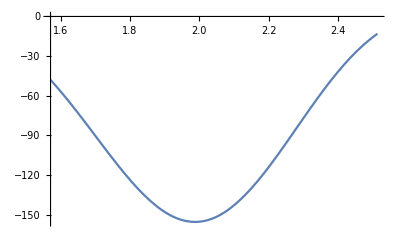

```mathematica
Plot[Re[P[Exp[I*θ]]]+2,{θ,Pi/2,4*Pi/5}]
```